# QMC Lookup Table Analysis

This Mathematica notebook is CF’s re-writing of the old Mathematica notebook that analyzes our data to fit the temperature.

Import packages to make legacy code work with newer version of mathematica (could update function calls but im lazy)

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["NumericalCalculus`"]
Needs["ErrorBarPlots`"]
```

## Introduction

## Constants

```mathematica
h=6.62607015 10^-34;
ℏ=h/(2π);
clight = 299792458.0; (*m/s*)
kB = 1.38064852 10^-23; (* boltzmann constant in J/K*)
amu=1.66054  10^-27; (*amu in kg*)
mK = 39.96399848 * amu;
mRb = 86.909180527 *amu;
μB =9.27401008 10^-24; (* Bohr magneton in A m^2*)
a0=5.29177210903 10^-11;(*bohr radius in meters*)

λlat=1054 10^-9;(* Lattice wavelength*)
klat=(2π)/λlat; (* lattice wavevector *)
dpx = 0.18 10^-6; (* Distance per pixel of the imaging system (?) *)
Er=(ℏ^2 klat^2)/(2 mK);(* recoil energy *)
```

## Settings and Helper Functions

```mathematica
co={RGBColor[0,0.4470,0.7410],
RGBColor[0.8500, 0.3250, 0.0980],
RGBColor[0.9290, 0.6940, 0.1250],
RGBColor[0.4940, 0.1840, 0.5560],
RGBColor[0.4660, 0.6740, 0.1880],
RGBColor[0.3010, 0.7450, 0.9330],
RGBColor[0.6350, 0.0780, 0.1840]};
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
```

## Trap Parameters

This portion of the code describes the physical parameters of the experiment.  This include the lattice depths and geometries, ODT depths and geometries, and magnetic field.

```mathematica
Show[Import[FileNameJoin[{NotebookDirectory[],"experiment_geometry.png"}]],ImageSize-> 300]
```

-Graphics-

From this we calculate the angles of the lattice and ODT and define them as unit vectors

```mathematica
θxdt1=57.15/180 π;θxdt2=29.24/180 π;θxlat=30.17/180 π;θylat=31.54/180 π;
vecxdt1=({{Cos[θxdt1]}, {-Sin[θxdt1]}});vecxlat=({{Sin[θxlat]}, {Cos[θxlat]}});vecylat=({{Cos[θylat]}, {-Sin[θylat]}});
```

### Lattice

This portion of the code defines the lattice parameters.

```mathematica
Vlatx=2.5;(* X Lattice depth in Er *)
Vlaty=Vlatx; (* Y Lattice depth in Er *)
Vlatz=Vlatx; (* Z Lattice depth in Er *)

w0x=60 10^-6; (* X Lattice waist *)
w0y=60 10^-6;  (* Y Lattice waist *)
w0z=85 10^-6; (* Z Lattice waist *)
bandnumber=6; (*?*)
```

And then calculate the angle of the lattice?

```mathematica
solangle=Solve[hh+kk*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])==Cos[θxdt1]*Sin[θxlat]-Sin[θxdt1]Cos[θxlat]&&
hh*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])+kk==Cos[θxdt1]*Cos[θylat]+Sin[θxdt1]Sin[θylat],{hh,kk}]
xdt1toxlat=solangle⟦1,1,2⟧;
xdt1toylat=solangle⟦1,2,2⟧;

(*do not project along one lattice direction.Assumption:isotropic cubic lattice (WHAT IS THIS FOR?)*)
xdt1toxlat=1;
xdt1toylat=0;
```

{{hh→-0.432367,kk→0.89142}}

Now calculate the harmonic confinement due to the envelope of lattice potential

```mathematica
fx=√(2/mK((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatz Er-√(Vlatz Er Er))/w0z^2))/(2π);
fy=√(2/mK((2Vlatz Er-√(Vlatz Er Er))/w0z^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π);
fz=√(2/mK((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π);
```

### Optical Dipole Trap

Define the trap frequency which is calibrated

```mathematica
xdt1=0.5; (* Power in optical dipole trap beam 1*)
fxdt=√(xdt1*1000)*3.29116-15.03525; (* Calculate the trap frequency based on calibrations *)
fxdt=32; (* Enforce it to a particular value *)
```

As long as the trap frequencies of the different XDT beams have been calibrated to be equal, the potential is rotationally symmetric. (1/2 mω^2 x^2+1/2 mω^2 y^2=1/2 mω^2 r^2)

### Total Trap Frequency

The total harmonic confinement is provided by both the confining XDT and the envelope of the lattice and is just the quadruture sum

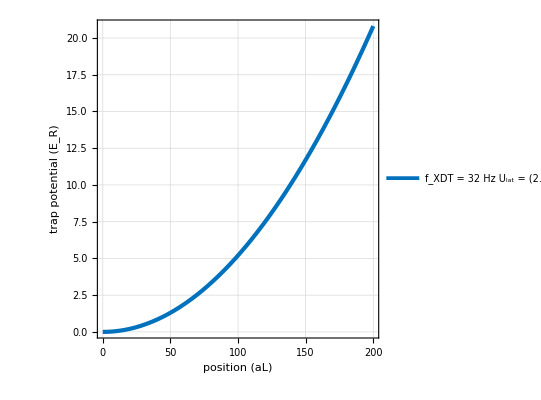

```mathematica
f0= √(fxdt^2+fx^2);
Utrap[x_]:=1/Er 1/2 mK (2π f0)^2(x λlat/2)^2;
s1="f_XDT = "   <>ToString[NumberForm[fxdt,3],StandardForm] <> " Hz \n " <> "U_lat = (" <>  ToString[NumberForm[Vlatx,3],StandardForm]  <> "," ToString[NumberForm[Vlatz,3],StandardForm]  <> "," <> ToString[NumberForm[Vlatx,3],StandardForm] <> ") E_R \n" <> "f_lat= " <> ToString[NumberForm[fx,3],StandardForm] <> " Hz";
Plot[Utrap[x],{x,0,200},PlotRange->{{0,200},Automatic},GridLines->Automatic,ImageSize->400,Frame->True,FrameLabel->{"position (aL)","trap potential (E_R)"},LabelStyle->Directive[16,Bold,Black],PlotStyle->{co[[1]],Thickness[.0075]},PlotLegends->Placed[LineLegend[{s1},LabelStyle->14],{Left,Top}],AspectRatio->1]
```

### Summarize

```mathematica
sData={{"XDT Frequency (Hz)",fxdt},
{"Lattice Depth (Er)",ToString[Vlatx] <> ", " <>ToString[Vlaty] <>", " <>ToString[Vlatz] },
{"Lattice Waists (μm)",ToString[NumberForm[N[w0x 10^6],3]] <> ", " <>ToString[NumberForm[N[w0y 10^6],3]] <>", " <>ToString[NumberForm[N[w0z 10^6],3]] },
{"Lattice Frequency (Hz)",ToString[NumberForm[N[fx],4]]}};
TextGrid[sData,Frame->All,Background->{{Gray,None},{None,None}}]
(*AutoCollapse[]*)
```

XDT Frequency (Hz) | 32
Lattice Depth (Er) | 2.5, 2.5, 2.5
Lattice Waists (μm) | 60., 60., 85.
Lattice Frequency (Hz) | 56.87

## Density Fitting

To perform the density fit, we analyze a radially averaged data sample at a specific lattice depth, external trap frequency, and magnetic field.

### Input Data

The input data is a text file of TSV data (tab separated values).  The first column is position (in pixels?), the second is the number of atoms, and the third is the error. I assume that the error comes from the radial averaging.

```mathematica
fdataname="2.5Er_206G/temp.txt";(*File location relative to notebook of the TSV data (tab separated values), (position,counts, error)*)

fdatanameFull=FileNameJoin[{NotebookDirectory[],fdataname}];
startid=12; (* 12; Start index to sample data (to avoid issues at the origin for radial data*)
aLMax=75; (* 60; Maximum lattice site to fit*)
```

Load the data in and convert it into lattice sites.

```mathematica
rawdatatemp=ToExpression[Import[fdatanameFull,"TSV"]]; (* Read in data file *)
datainput1=Table[{rawdatatemp⟦ii,1⟧dpx/(λlat/2),rawdatatemp⟦ii,2⟧,rawdatatemp⟦ii,3⟧},{ii,startid,Length[rawdatatemp]}]; (* Convert pixel position to lattice sites *)
datainput=Select[datainput1,#⟦1⟧≤ aLMax&];
```

Plot the initial data.

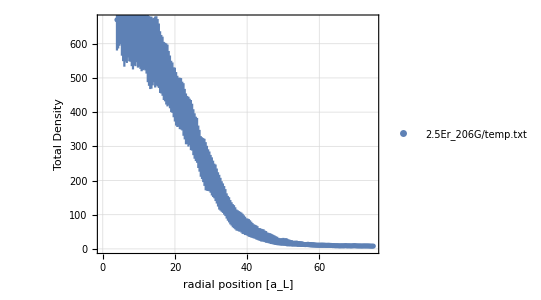

```mathematica
ErrorListPlot[datainput,GridLines->Automatic,ImageSize->400,Frame->True,FrameLabel->{"radial position [a_L]","Total Density"},LabelStyle->Directive[16,Bold,Black],AspectRatio->0.75,PlotLegends->Placed[LineLegend[{fdataname},LabelStyle->18],{Right,Top}]]
```

### Import Fit Data Table

The fit comes from using lookup tables outputted by the QUEST QMC analysis that is done ahead of time. The results of the QMC calculation for varying temperature is stored in a text file. 

The fit output is report as (Nx6) data matrix. It is organized as (temperature (β),singlon density, singlon density error,double density, dublon density error) 

(temperature (β),chemical potential, total density, total density error,doublon density, dublon density error)

So the singlon density (what we image)

total density - 2* doublon density

Due to issues with brightness calibration, we let the absolute density scale freely.

Import the data.

```mathematica
ffitname="2.5Er_206G/results.txt";
fitdata=ToExpression[Import[ffitname,"TSV"]];
```

Display a list of all temperatures that are included in the calculations (in units of β).

```mathematica
tempβlist=Union[fitdata⟦All,1⟧];
tempβnum=Length[tempβlist];
```

### Do the Fit

To perform the fit, we first fit the data for all temperatures

Iteration 1 : β = 1.01833

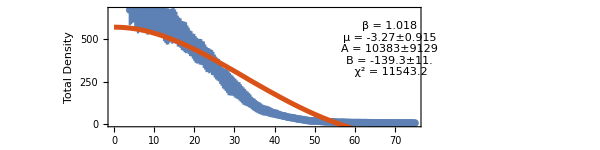

Iteration 2 : β = 1.0627

InterpolatingFunction::dmval: Input value {-7.03863} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.06509} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

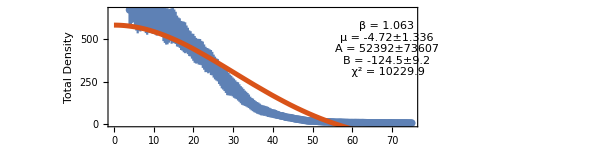

Iteration 3 : β = 1.11111

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

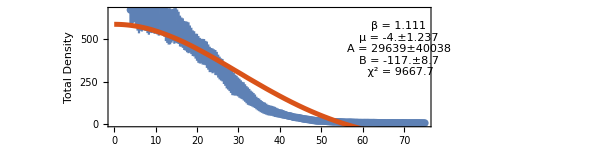

Iteration 4 : β = 1.16414

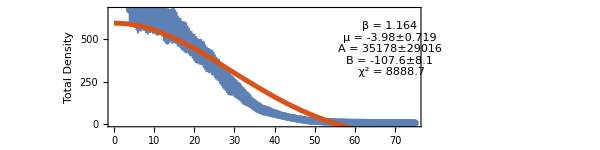

Iteration 5 : β = 1.22249

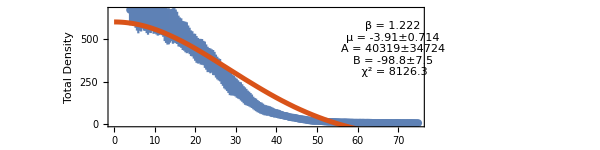

Iteration 6 : β = 1.287

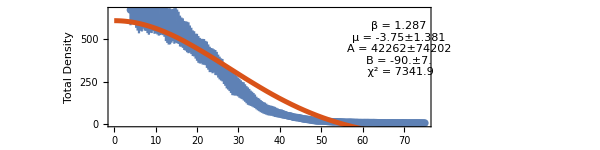

Iteration 7 : β = 1.3587

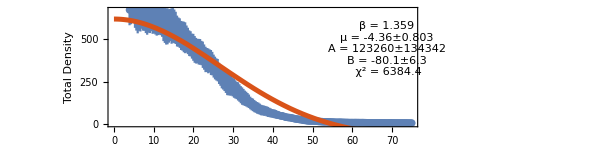

Iteration 8 : β = 1.43885

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

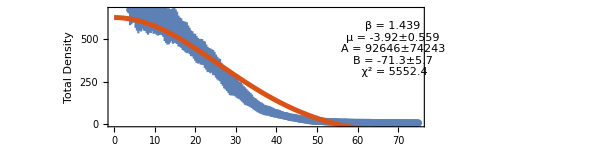

Iteration 9 : β = 1.52905

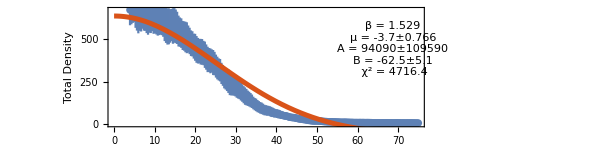

Iteration 10 : β = 1.63132

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

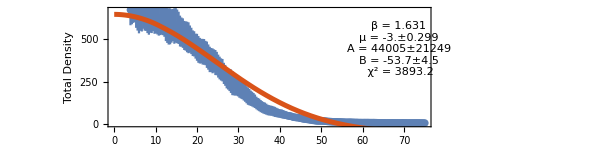

Iteration 11 : β = 1.74825

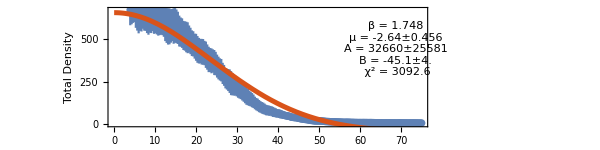

Iteration 12 : β = 1.88324

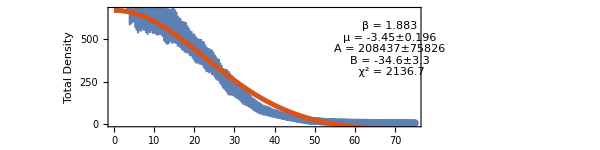

Iteration 13 : β = 2.04082

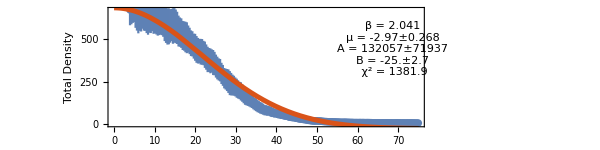

Iteration 14 : β = 2.22717

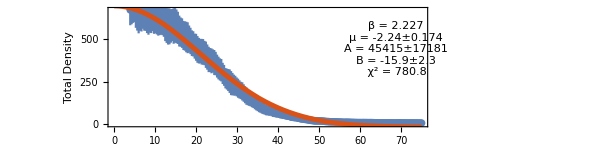

Iteration 15 : β = 2.45098

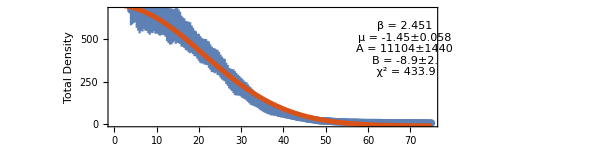

Iteration 16 : β = 2.7248

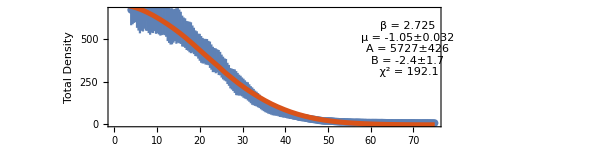

Iteration 17 : β = 3.06748

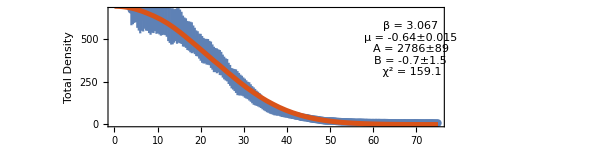

Iteration 18 : β = 3.50877

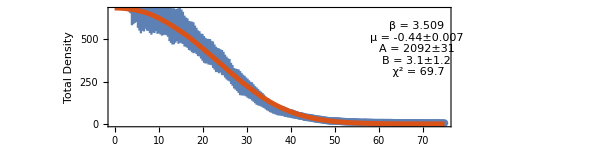

Iteration 19 : β = 4.09836

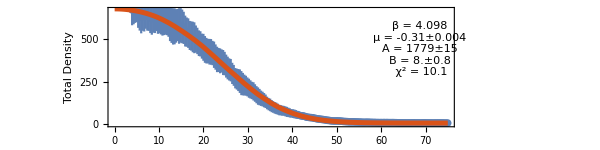

Iteration 20 : β = 4.92611

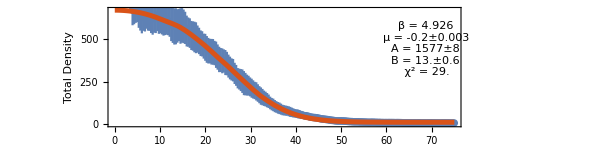

Iteration 21 : β = 6.17284

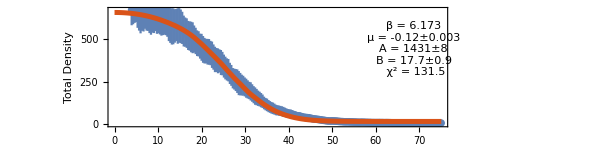

Iteration 22 : β = 8.26446

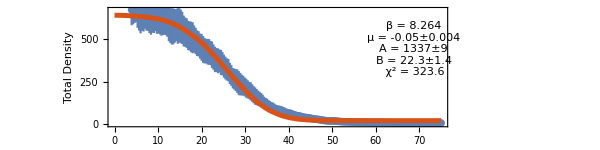

```mathematica
fitls={};
tempβlist=Union[fitdata⟦All,1⟧];
tempβnum=Length[tempβlist];
For[iitempβ=1,iitempβ≤tempβnum,iitempβ++,
{
Clear[densitycheckfunc,densityerrcheckfunc,doubloncheckfunc,doublonerrcheckfunc,finalρfunc,finalρerrfunc,xx,μ,A,B];
tempβcheck=tempβlist⟦iitempβ⟧; (* This temperature *)
Print["Iteration " <> ToString[iitempβ] <> " : β = "  <> ToString[tempβcheck]];

(* Get all the data associated with this temperaure *)
Tβlist= Select[fitdata,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧; 

(* Create Interpolant function (in position) for each observable *)
densitycheckfunc=Interpolation[Tβlist⟦All,{2,3}⟧];  
densityerrcheckfunc=Interpolation[Tβlist⟦All,{2,4}⟧];
doubloncheckfunc=Interpolation[Tβlist⟦All,{2,5}⟧];
doublonerrcheckfunc=Interpolation[Tβlist⟦All,{2,6}⟧];

(* From interpolants, make the fit functions which include offsets, amplitudes, and chemical potentials; Local density approximation *)
finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=ampxx*(densitycheckfunc[μfitxx-Utrap[positionxx]]-2doubloncheckfunc[μfitxx-Utrap[positionxx]])+offsetxx;
finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*√(densityerrcheckfunc[μfitxx-Utrap[positionxx]]^2+4 doublonerrcheckfunc[μfitxx-Utrap[positionxx]]^2);

(* Create initial guess *)
μGuess=-1;(* Chemical potential *)
AGuess=Max[datainput⟦All,2⟧]/(densitycheckfunc[μGuess]-2doubloncheckfunc[μGuess]); (* Amplitude *)

BGuess=Min[datainput⟦All,2⟧]; (* background level *)

sol=NonlinearModelFit[datainput⟦All,{1,2}⟧,finalρfunc[xx,μ,A,B],{{μ,μGuess},{A,AGuess},{B,BGuess}},xx];

(* Extract the Fit Parameters *)
sol1=sol["ParameterTable"];
μfit=sol1⟦1,1,2,2⟧;
ampfit=sol1⟦1,1,3,2⟧;
offsetfit=sol1⟦1,1,4,2⟧;
μfiterr=sol1⟦1,1,2,3⟧;
ampfiterr=sol1⟦1,1,3,3⟧;
offsetfiterr=sol1⟦1,1,4,3⟧;

(* Calculate χ^2 *)
χlist=Table[(finalρfunc[datainput⟦ii,1⟧,μfit,ampfit,offsetfit]- datainput⟦ii,2⟧ )^2/1/(datainput⟦ii,3⟧^2+finalρerrfunc[datainput⟦ii,1⟧,μfit,1 ]^2),{ii,startid,Length[datainput]}];
χsquare=Total[χlist];

(* Make Strings for Plotting *)

βstr="β = " <> ToString[Round[tempβcheck,.001]];
μstr="μ = " <> ToString[Round[μfit,.01]] <> "±" <> ToString[Round[μfiterr,.001]];
Astr="A = " <> ToString[Round[ampfit]] <> "±" <> ToString[Round[ampfiterr]];
Bstr="B = " <> ToString[Round[offsetfit,.1]] <> "±" <> ToString[Round[offsetfiterr,.1]];
χstr="χ^2 = " <> ToString[Round[χsquare,.1]];
pStr=βstr <> "\n" <> μstr <> "\n" <> Astr  <> "\n" <> Bstr <> "\n" χstr;

(* Plot the data and the fit *)

Print[Show[ErrorListPlot[datainput],Plot[finalρfunc[x,μfit,ampfit,offsetfit],{x,0,aLMax},PlotStyle->{co[[2]],Thickness[.006]}],ImageSize->600,Frame->True,FrameLabel->{"radial position [a_L]","Total Density"},LabelStyle->Directive[12,Black],AspectRatio->0.25,Epilog->{Style[Text[pStr,Scaled[{.9,.65}]],10]}]];


(* Join fit information to the output list *)
fitlstemp={{tempβcheck,μfit,ampfit,offsetfit,χsquare,μfiterr,ampfiterr,offsetfiterr}};
fitls=Join[fitls,fitlstemp];
}
]
```

We then look at the χ^2 value for the different temperatures, and then do some estimations on it

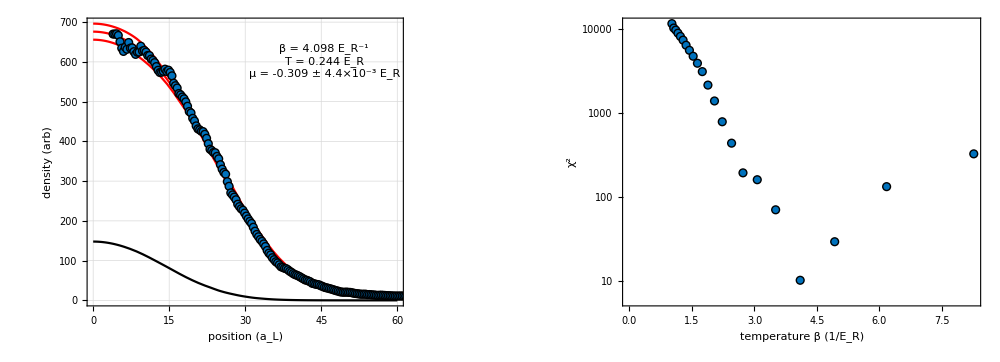

```mathematica
mymarker[in_,out_: Black,size_: 8]:=Graphics[{in,EdgeForm[{AbsoluteThickness[1],out}],Disk[]},PlotRangePadding->0,ImageSize->size]

pchi=ListLogPlot[fitls⟦All,{1,5}⟧,GridLines->Automatic,ImageSize->400,Frame->True,FrameLabel->{"temperature β (1/E_R)","χ^2"},LabelStyle->Directive[14,Bold,Black],AspectRatio->.75,PlotMarkers->mymarker/@{co⟦1⟧,Green,Blue}];

fitBest=Sort[fitls,#1⟦5⟧<#2⟦5⟧&]⟦1⟧;

βFit=fitBest⟦1⟧;
μFit=fitBest⟦2⟧;
AFit=fitBest⟦3⟧;
BFit=fitBest⟦4⟧;
μFiterr=fitBest⟦6⟧;
AFiterr=fitBest⟦7⟧;
BFiterr=fitBest⟦8⟧;

(* Get all the data associated with this temperaure *)
Tβlist2= Select[fitdata,#⟦1⟧==βFit&]⟦All,1;;6⟧; 

(* Create Interpolant function (in position) for each observable *)
densitycheckfunc=Interpolation[Tβlist2⟦All,{2,3}⟧];  
densityerrcheckfunc=Interpolation[Tβlist2⟦All,{2,4}⟧];
doubloncheckfunc=Interpolation[Tβlist2⟦All,{2,5}⟧];
doublonerrcheckfunc=Interpolation[Tβlist2⟦All,{2,6}⟧];

(* From interpolants, make the fit functions which include offsets, amplitudes, and chemical potentials; Local density approximation *)
ρFit[xx_,μ_,A_,B_]:=A*(densitycheckfunc[μ-Utrap[xx]]-2doubloncheckfunc[μ-Utrap[xx]])+B;
ρFitErr[xx_,μ_,A_]:=A*√(densityerrcheckfunc[μ-Utrap[xx]]^2+4 doublonerrcheckfunc[μ-Utrap[xx]]^2);
ρ2Fit[xx_,μ_,A_]:=A*doubloncheckfunc[μ-Utrap[xx]]


βstr="β = " <> ToString[Round[βFit,.001]] <> " E_R^-1";
Tstr="T = " <> ToString[Round[1/βFit,.001]] <> " E_R";
μstr="μ = " <> ToString[Round[μFit,.001]] <> " ± " <> ToString[ScientificForm[μFiterr,2],TraditionalForm]<> " E_R";
Astr="A = " <> ToString[Round[AFit]] <> " ± " <> ToString[Round[AFiterr]] ;
pStr=βstr <> "\n" <> Tstr <> "\n" <> μstr;


p1=Show[Plot[{ρFit[x,μFit,AFit,BFit],ρFit[x,μFit,AFit,BFit]-ρFitErr[x,μFit,AFit],ρFit[x,μFit,AFit,BFit]+ρFitErr[x,μFit,AFit],ρ2Fit[x,μFit,AFit]},{x,0,60},PlotStyle->{Red,Red,Red,Black}],ListPlot[datainput⟦All,{1,2}⟧,PlotMarkers->mymarker/@{co⟦1⟧,Green,Blue}],Epilog->{Style[Text[pStr,Scaled[{.75,.85}]],14,Bold]},GridLines->Automatic,ImageSize->400,Frame->True,FrameLabel->{"position (a_L)","density (arb)"},LabelStyle->Directive[14,Bold,Black],AspectRatio->.75];

GraphicsRow[{p1,pchi},ImageSize-> 1000]
```

```mathematica
Export["C:\\Users\\coraf\\Documents\\GitHub\\QMCLookup\\2.5Er_206G\\2.5Er_206G.png",%548,"PNG"]
```

C:\Users\coraf\Documents\GitHub\QMCLookup\2.5Er_206G\2.5Er_206G.png